# Computational Science

## Machine Learning for Physicists Project: Unsupervised and supervised analysis of protein sequences

This notebook is 100% human-made and has been created without the help of any LLM.

Paul Cousin

Université Paris Cité • Master’s Physics Of Complex Systems • 2025/2026

## Note to the reader

Cells colored in blue will be code cells.

Cells colored in pink will be text comments.

## Import and format data

```mathematica
formatData[s_String]:=Module[{string=s},
string//=StringSplit[#,">"]&;
string//=StringDelete[#,"\n"]&;
string//=StringReplace[#,"sequence_"~~x:NumberString~~" functional_"~~y:("true"|"false")~~z__~~WordBoundary:>x~~","~~y~~","~~z]&;string//=StringSplit[#,","]&;
string/.{x_,y_,z_}:>{ToExpression@x,y=="true",z}
];
```

formatData is a function that formats the content of the .faa files which is encapsulated in  and  in the following cell.

```mathematica
naturalSequences=formatData@;
artificialSequences=formatData@;
```

Here is an example of how a sequence is now formatted.

```mathematica
naturalSequences[[1]]
```

{1,True,-TSENPLLALREKISALDEKLLALLAERRELAVEVGKAKLLSHRPVRDIDRERDLLERLITLGK-AHHLDAHYITRLFQLIIEDSVLTQQALLQQH}

## Task 1: One-hot encoding of protein sequence data

Let’s encode our sequences using one-hot encoding.

```mathematica
characterMap={"A"->1,"C"->2,"D"->3,"E"->4,"F"->5,"G"->6,"H"->7,"I"->8,"K"->9,"L"->10,"M"->11,"N"->12,"P"->13,"Q"->14,"R"->15,"S"->16,"T"->17,"V"->18,"W"->19,"Y"->20};
```

```mathematica
oneHotEncode[seq_]:=SparseArray[If[#!="-",#->1,{}],20]&/@Replace[characterMap]/@StringPartition[seq,1];
```

```mathematica
naturalSequencesOneHot=Flatten/@SparseArray[oneHotEncode/@naturalSequences[[;;,3]]];
artificialSequencesOneHot=Flatten/@SparseArray[oneHotEncode/@artificialSequences[[;;,3]]];
```

All the sequences have been one-hot encoded in the SparseArray format, and reshaped to vector columns for the purpose of future computations.

## Task 2: Dimensional reduction and visualization of sequence space

Let’s compute the covariance matrix. Here, the number of features is not really the length of the vector but rather the original length of the sequence, since it is the maximum number of 1 that can appear in the vector. Our sequences are at most 96 base-pair long.

```mathematica
covarianceMatrixNatural=(#ᵀ.#)/95.&@naturalSequencesOneHot;
```

Using the first eigenvalues and eigenvectors of this covariance matrix, we can project our data on the two or three most meaningful axes. For this purpose we can use the Eigenvectors function which will return the first eigenvectors sorted by eigenvalues. Here we will compute only three.

```mathematica
eigenvectorsNatural=Eigenvectors[covarianceMatrixNatural,3];
```

```mathematica
projectedNaturalSequences=naturalSequencesOneHot.eigenvectorsNaturalᵀ;
```

To separate the functional and non-functional sequence, we need the indices corresponding to each.

```mathematica
funtionalNaturalIndices=Cases[naturalSequences,x_?(#[[2]]&):>x[[1]]];
nonFuntionalNaturalIndices=Complement[Range@Length@naturalSequences,funtionalNaturalIndices];
funtionalArtificialIndices=Cases[artificialSequences,x_?(#[[2]]&):>x[[1]]];
nonFuntionalArtificialIndices=Complement[Range@Length@artificialSequences,funtionalArtificialIndices];
```

Let’s plot the result, first in 2D.

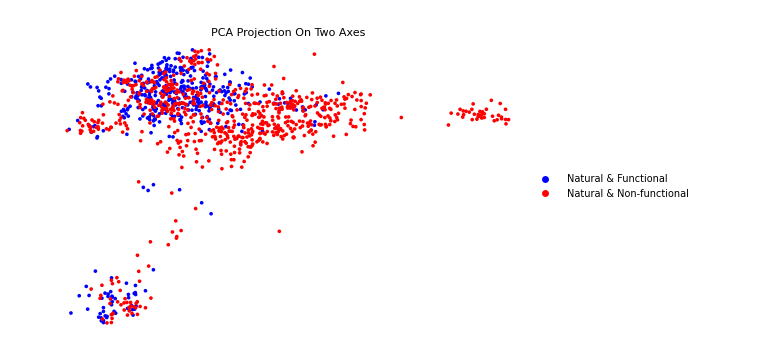

```mathematica
plotNatural2D=ListPlot[
projectedNaturalSequences[[#,;;2]]&/@{funtionalNaturalIndices,nonFuntionalNaturalIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Blue,Red},PlotLabel->"PCA Projection On Two Axes",PlotLegends-> {"Natural & Functional","Natural & Non-functional"}]
```

The following 3D plot is interactive and can be manipulated.

```mathematica
plotNatural3D=ListPointPlot3D[
projectedNaturalSequences[[#]]&/@{funtionalNaturalIndices,nonFuntionalNaturalIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Blue,Red},PlotLabel->"PCA Projection On Three Axes",PlotLegends-> {"Natural & Functional","Natural & Non-functional"}]
```

-Graphics3D-

Let’s now look at the artificial sequences projected on the previously computed vectors.

```mathematica
projectedArtificialSequences=artificialSequencesOneHot.eigenvectorsNaturalᵀ;
```

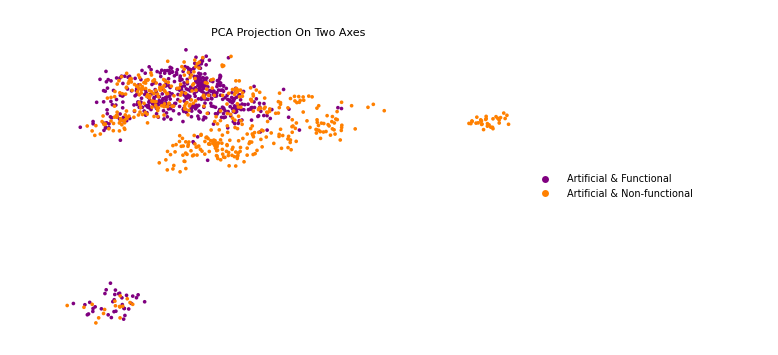

```mathematica
plotArtificial2D=ListPlot[projectedArtificialSequences[[#,;;2]]&/@{funtionalArtificialIndices,nonFuntionalArtificialIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Purple,Orange},PlotLabel->"PCA Projection On Two Axes",PlotLegends-> {"Artificial & Functional","Artificial & Non-functional"}]
```

```mathematica
plotArtificial3D=ListPointPlot3D[projectedArtificialSequences[[#]]&/@{funtionalArtificialIndices,nonFuntionalArtificialIndices},
Axes->False,PlotRange->Full,ImageSize->Large,PlotStyle->{Purple,Orange},PlotLabel->"PCA Projection On Three Axes",PlotLegends-> {"Artificial & Functional","Artificial & Non-functional"}]
```

-Graphics3D-

Natural and artificial sequences seem to follow similar distributions. To be sure, let’s plot both together.

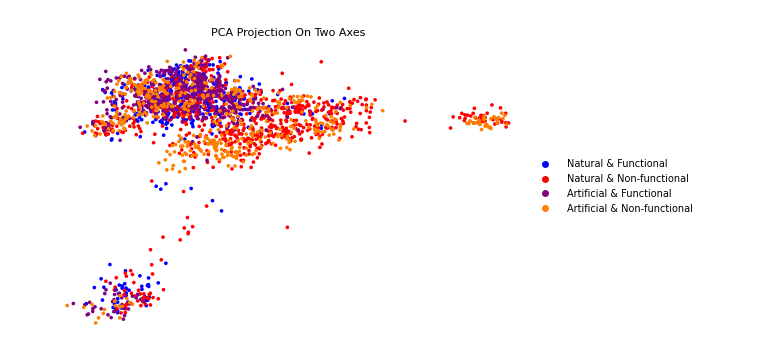

```mathematica
Show[{plotNatural2D,plotArtificial2D},PlotRange->All]
```

```mathematica
Show[{plotNatural3D,plotArtificial3D},PlotRange->All]
```

-Graphics3D-

In the case of both natural and artificial sequences, we see regions that are clearly non-functional and other regions in which a mixture of functional and non-functional sequences coexist.

## Task 3: Clustering sequence data

Here is a simple implementation of the k-means algorithm.

```mathematica
kMeans[data_,numberOfClusters_,iterations_]:=Module[{assignments,indices,means,objective={}},
assignments=RandomInteger[{1,numberOfClusters},Length@data];
indices=Catenate[Position[assignments,#]]&/@Range[numberOfClusters];
Do[
means=N@Mean@data[[#]]&/@indices;
assignments=Catenate[PositionSmallest/@(Table[Norm[#-means[[n]]],{n,numberOfClusters}]&/@data)];
AppendTo[objective,Total@Table[Norm[data[[n]]-means[[assignments[[n]]]]],{n,Length@data}]];
indices=Catenate[Position[assignments,#]]&/@Range[numberOfClusters];,
iterations];
{ListPlot[objective,PlotRange->All,PlotLabel->"Objective function"],indices,assignments}
];
```

We will use it first on the natural sequences only.

### K-means with 3 clusters

```mathematica
natural3Clusters=kMeans[naturalSequencesOneHot,3,30];
```

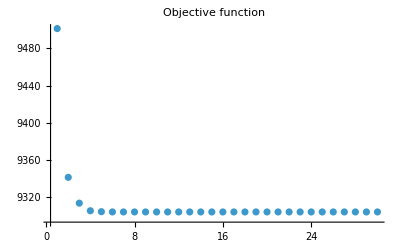

```mathematica
natural3Clusters[[1]]
```

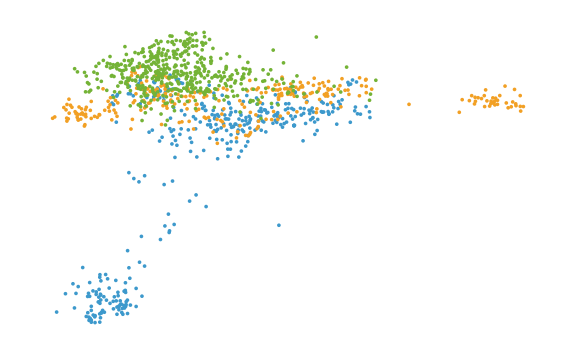

```mathematica
ListPlot[projectedNaturalSequences[[#,;;2]]&/@natural3Clusters[[2]],
Axes->False,PlotRange->Full,ImageSize->Large]
```

```mathematica
PairedBarChart[
Length[#∩funtionalNaturalIndices]&/@natural3Clusters[[2]],
Length[#∩nonFuntionalNaturalIndices]&/@natural3Clusters[[2]]
,ChartLegends->{{"Natural & Functional","Natural & Non-functional"},None,None},ChartStyle->{"Pastel",None,None}]
```

-Graphics-

### K-means with 5 clusters

```mathematica
natural5Clusters=kMeans[naturalSequencesOneHot,5,30];
```

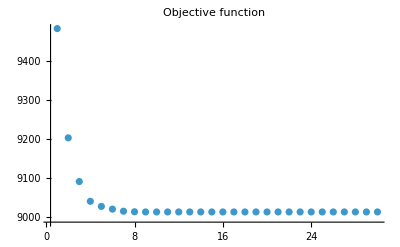

```mathematica
natural5Clusters[[1]]
```

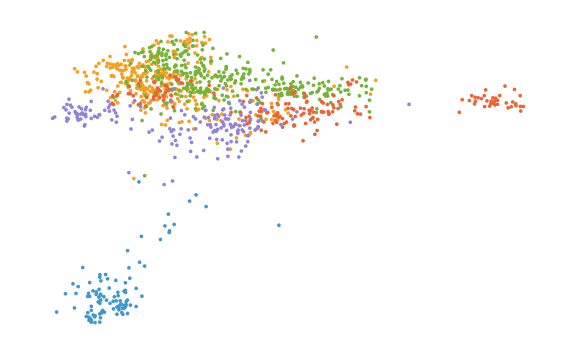

```mathematica
ListPlot[projectedNaturalSequences[[#,;;2]]&/@natural5Clusters[[2]],
Axes->False,PlotRange->Full,ImageSize->Large]
```

```mathematica
PairedBarChart[
Length[#∩funtionalNaturalIndices]&/@natural5Clusters[[2]],
Length[#∩nonFuntionalNaturalIndices]&/@natural5Clusters[[2]]
,ChartLegends->{{"Natural & Functional","Natural & Non-functional"},None,None},ChartStyle->{"Pastel",None,None}]
```

-Graphics-

### K-means with 20 clusters

```mathematica
natural20Clusters=kMeans[naturalSequencesOneHot,20,30];
```

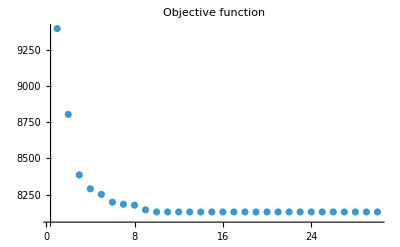

```mathematica
natural20Clusters[[1]]
```

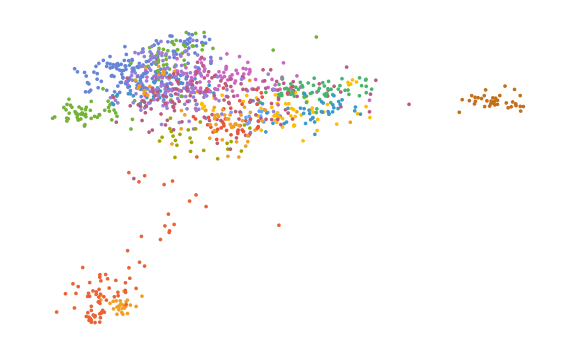

```mathematica
ListPlot[projectedNaturalSequences[[#,;;2]]&/@natural20Clusters[[2]],
Axes->False,PlotRange->Full,ImageSize->Large]
```

```mathematica
PairedBarChart[#1,#2,
ChartLegends->{{"Natural & Functional","Natural & Non-functional"},None,None},ChartStyle->{"Pastel",None,None}
]&@@(SortBy[{Length[#∩funtionalNaturalIndices]&/@natural20Clusters[[2]],
Length[#∩nonFuntionalNaturalIndices]&/@natural20Clusters[[2]]}ᵀ,#[[2]]&]ᵀ)
```

-Graphics-

### K-means with 100 clusters

```mathematica
natural100Clusters=kMeans[naturalSequencesOneHot,100,30];
```

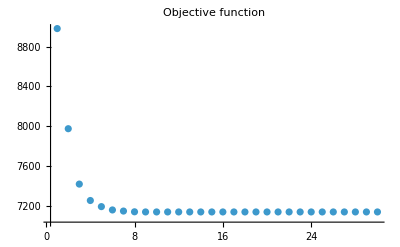

```mathematica
natural100Clusters[[1]]
```

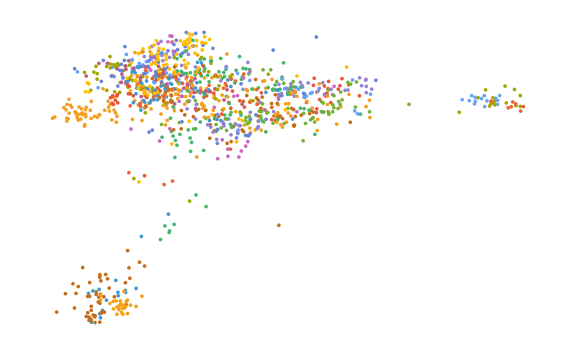

```mathematica
ListPlot[projectedNaturalSequences[[#,;;2]]&/@natural100Clusters[[2]],
Axes->False,PlotRange->Full,ImageSize->Large]
```

```mathematica
PairedBarChart[#1,#2,
ChartLegends->{{"Natural & Functional","Natural & Non-functional"},None,None},ChartStyle->{"Pastel",None,None}
]&@@(SortBy[{Length[#∩funtionalNaturalIndices]&/@natural100Clusters[[2]],
Length[#∩nonFuntionalNaturalIndices]&/@natural100Clusters[[2]]}ᵀ,#[[2]]&]ᵀ)
```

-Graphics-

## Task 4: Predicting protein functionality

## Task 5: Generating artificial sequences

Idea: use a variational auto-encoder

LOSS = (X-reconstruction)^2 + μ^2 + (σ^2+log^2 σ-1)

μ = norm of the vector (to enforce that the means are close to 0) 
σ = variance



Look at conditional variational autoencoder

```mathematica
Dimensions[naturalSequencesOneHot][[2]]
```

1920

```mathematica
layers={1920,1080,512,256,128,64,64,128,256,512,1080,1920};
```

```mathematica
matrices=Table[RandomReal[{0,1},{layers[[i]],layers[[i+1]]}],{i,Length@layers-1}];
```

```mathematica
Max[x,0];
```

```mathematica
HeavisideTheta[x];
```

```mathematica
Dimensions[Dot@@Prepend[matrices,naturalSequencesOneHot[[1]]]]
```

{1920}

```mathematica
Fold[Max[0,#1.#2]&,x,{a,b,c}]
```

Max[0,Max[0,Max[0,x.a].b].c]

```mathematica
relu[x_]:=Max[0,x];
```

```mathematica
Fold[relu/@#1.#2&,naturalSequencesOneHot[[1]],matrices]
```

{6.13439×10^22,5.97476×10^22,6.13205×10^22,6.22695×10^22,5.94259×10^22,5.96274×10^22,5.98244×10^22,6.31533×10^22,5.96061×10^22,6.06196×10^22,6.21798×10^22,6.10375×10^22,6.01847×10^22,6.10505×10^22,6.12588×10^22,6.10623×10^22,5.94695×10^22,5.99883×10^22,5.98446×10^22,5.92995×10^22,5.93202×10^22,6.12988×10^22,6.01527×10^22,6.0691×10^22,6.05361×10^22,6.046×10^22,6.24301×10^22,6.13711×10^22,6.09438×10^22,5.88258×10^22,5.97219×10^22,6.20109×10^22,6.04781×10^22,6.20377×10^22,6.06965×10^22,5.90365×10^22,5.90463×10^22,6.0909×10^22,5.96642×10^22,6.045×10^22,5.95783×10^22,6.04672×10^22,6.08194×10^22,6.02743×10^22,5.96607×10^22,6.02042×10^22,5.99694×10^22,5.86288×10^22,6.09514×10^22,5.87054×10^22,5.95325×10^22,5.96473×10^22,6.15842×10^22,5.97985×10^22,5.93219×10^22,6.06087×10^22,5.99096×10^22,6.056×10^22,6.01791×10^22,6.13608×10^22,5.915×10^22,5.95543×10^22,6.09932×10^22,6.10859×10^22,6.1946×10^22,5.91281×10^22,6.02552×10^22,6.02127×10^22,6.00631×10^22,5.96518×10^22,6.17519×10^22,6.04632×10^22,6.03644×10^22,6.04823×10^22,6.12196×10^22,6.22679×10^22,6.16305×10^22,5.99287×10^22,5.96778×10^22,5.98164×10^22,6.04983×10^22,6.13484×10^22,6.07666×10^22,6.08345×10^22,6.17369×10^22,6.30533×10^22,6.15119×10^22,6.1706×10^22,6.23745×10^22,6.0907×10^22,6.00512×10^22,6.07555×10^22,5.95668×10^22,6.26174×10^22,6.22214×10^22,6.07088×10^22,6.05746×10^22,5.93657×10^22,5.9705×10^22,6.21215×10^22,5.89581×10^22,6.08959×10^22,6.12483×10^22,5.82442×10^22,6.28828×10^22,5.94707×10^22,6.06294×10^22,6.16032×10^22,5.82303×10^22,5.95866×10^22,6.13047×10^22,5.8503×10^22,6.12758×10^22,6.00269×10^22,6.11281×10^22,6.02499×10^22,5.91218×10^22,6.09128×10^22,5.89573×10^22,5.96247×10^22,6.20032×10^22,6.02934×10^22,5.99481×10^22,6.03413×10^22,6.04404×10^22,6.03454×10^22,6.11657×10^22,6.02394×10^22,6.02855×10^22,6.19688×10^22,6.20092×10^22,6.10398×10^22,5.90737×10^22,6.20097×10^22,5.84174×10^22,6.0159×10^22,5.94957×10^22,6.03444×10^22,6.02009×10^22,5.86413×10^22,6.20306×10^22,6.05179×10^22,6.01155×10^22,6.14166×10^22,6.06225×10^22,5.99241×10^22,6.21125×10^22,6.16325×10^22,6.16225×10^22,6.11362×10^22,5.91701×10^22,5.82097×10^22,6.19458×10^22,5.78104×10^22,6.12102×10^22,6.06388×10^22,6.29085×10^22,6.41452×10^22,6.06236×10^22,5.93003×10^22,6.04875×10^22,6.09723×10^22,6.26425×10^22,6.10574×10^22,6.08152×10^22,6.03604×10^22,6.08887×10^22,5.95096×10^22,5.97833×10^22,6.11843×10^22,6.15331×10^22,5.96779×10^22,6.04519×10^22,6.04782×10^22,6.08623×10^22,6.05294×10^22,6.27115×10^22,6.16001×10^22,6.25084×10^22,6.08755×10^22,6.16157×10^22,6.142×10^22,6.18147×10^22,5.98474×10^22,6.09727×10^22,6.08406×10^22,6.23513×10^22,6.04873×10^22,6.01108×10^22,6.01987×10^22,6.05725×10^22,6.06511×10^22,6.12323×10^22,6.13487×10^22,6.02707×10^22,6.26568×10^22,6.21107×10^22,6.10176×10^22,6.04856×10^22,6.10023×10^22,6.07815×10^22,6.25919×10^22,6.07157×10^22,5.86517×10^22,6.11235×10^22,6.01808×10^22,6.10353×10^22,6.21949×10^22,6.02201×10^22,6.10151×10^22,6.00545×10^22,6.00239×10^22,6.14034×10^22,6.13441×10^22,6.05039×10^22,6.09662×10^22,6.09309×10^22,6.1772×10^22,5.91618×10^22,6.12868×10^22,6.23931×10^22,6.09812×10^22,5.86249×10^22,6.16598×10^22,6.11256×10^22,6.08756×10^22,6.01992×10^22,5.91043×10^22,6.13052×10^22,6.1446×10^22,6.18505×10^22,6.03625×10^22,6.01381×10^22,6.13213×10^22,5.96535×10^22,6.04505×10^22,5.88408×10^22,6.21164×10^22,5.97518×10^22,6.20216×10^22,6.04973×10^22,6.09884×10^22,5.8434×10^22,6.02122×10^22,6.19382×10^22,6.24468×10^22,5.98538×10^22,6.34387×10^22,6.20059×10^22,5.9592×10^22,6.1567×10^22,5.96552×10^22,6.12106×10^22,6.05011×10^22,6.26084×10^22,5.82488×10^22,6.22227×10^22,5.9318×10^22,6.2173×10^22,6.15188×10^22,5.94998×10^22,5.92503×10^22,5.87248×10^22,6.01715×10^22,6.02748×10^22,6.10637×10^22,6.20663×10^22,6.05878×10^22,5.82021×10^22,5.92741×10^22,6.12336×10^22,6.12229×10^22,6.0727×10^22,5.89521×10^22,6.22926×10^22,6.12619×10^22,6.06816×10^22,6.07036×10^22,6.19871×10^22,6.05405×10^22,5.91058×10^22,6.12667×10^22,6.3054×10^22,6.08103×10^22,6.12905×10^22,5.99945×10^22,6.18686×10^22,5.9549×10^22,6.12547×10^22,6.09537×10^22,6.08264×10^22,6.16735×10^22,6.10151×10^22,6.09044×10^22,5.98589×10^22,6.0699×10^22,5.961×10^22,5.95646×10^22,6.07888×10^22,6.10505×10^22,5.96091×10^22,6.34167×10^22,5.99945×10^22,6.14241×10^22,6.19349×10^22,5.99899×10^22,6.02362×10^22,6.11524×10^22,6.0555×10^22,5.80994×10^22,6.17551×10^22,6.12848×10^22,6.06181×10^22,6.06022×10^22,6.11739×10^22,6.16707×10^22,6.11302×10^22,6.06674×10^22,6.09064×10^22,6.00661×10^22,6.37849×10^22,6.20312×10^22,5.9281×10^22,6.11798×10^22,6.05746×10^22,6.28499×10^22,6.21564×10^22,5.92851×10^22,5.97951×10^22,5.97721×10^22,6.0479×10^22,6.11777×10^22,6.18063×10^22,6.1832×10^22,6.03622×10^22,5.99503×10^22,6.22198×10^22,6.12218×10^22,6.10351×10^22,6.09157×10^22,6.19918×10^22,5.85466×10^22,6.00171×10^22,5.98551×10^22,6.02354×10^22,6.0935×10^22,5.96366×10^22,6.1303×10^22,6.1904×10^22,5.94079×10^22,6.04509×10^22,6.08329×10^22,6.11374×10^22,6.17095×10^22,6.05034×10^22,6.13165×10^22,5.94904×10^22,5.91455×10^22,6.13797×10^22,5.94879×10^22,6.12817×10^22,6.06708×10^22,6.13625×10^22,6.28337×10^22,6.01659×10^22,6.17469×10^22,5.84265×10^22,6.04471×10^22,6.12723×10^22,6.0823×10^22,6.03789×10^22,6.0853×10^22,6.08742×10^22,5.97136×10^22,5.96083×10^22,6.08108×10^22,6.30927×10^22,6.17204×10^22,5.8773×10^22,5.84615×10^22,6.06455×10^22,6.08806×10^22,6.31425×10^22,6.15575×10^22,6.1314×10^22,6.04406×10^22,6.13012×10^22,6.10781×10^22,6.09268×10^22,6.05406×10^22,5.95108×10^22,5.8597×10^22,6.11321×10^22,6.1498×10^22,5.92304×10^22,5.99954×10^22,6.00037×10^22,6.17872×10^22,5.98416×10^22,6.12031×10^22,6.10402×10^22,6.16438×10^22,6.13363×10^22,6.01186×10^22,6.09695×10^22,5.93625×10^22,5.99026×10^22,6.07682×10^22,6.02412×10^22,6.03102×10^22,6.03195×10^22,5.84426×10^22,5.97245×10^22,6.02027×10^22,6.09124×10^22,6.15105×10^22,5.86667×10^22,6.12084×10^22,5.84068×10^22,6.06334×10^22,6.15431×10^22,6.14332×10^22,6.11981×10^22,6.12307×10^22,6.13479×10^22,6.17675×10^22,6.12091×10^22,5.93045×10^22,6.31234×10^22,6.05896×10^22,5.96473×10^22,6.12452×10^22,6.09723×10^22,5.95677×10^22,5.98509×10^22,6.02405×10^22,6.04443×10^22,6.09504×10^22,6.12929×10^22,6.104×10^22,5.97172×10^22,6.12904×10^22,6.01794×10^22,6.10715×10^22,6.05775×10^22,6.1364×10^22,6.08039×10^22,6.02285×10^22,5.9225×10^22,6.03964×10^22,6.02951×10^22,6.06207×10^22,5.81385×10^22,5.97473×10^22,6.09913×10^22,5.99443×10^22,6.32814×10^22,5.99536×10^22,6.216×10^22,6.02703×10^22,6.00998×10^22,6.01454×10^22,6.09544×10^22,5.96263×10^22,6.15065×10^22,6.0585×10^22,5.96282×10^22,6.04609×10^22,6.24531×10^22,6.02875×10^22,6.13377×10^22,5.96423×10^22,6.13674×10^22,6.04649×10^22,6.01292×10^22,5.92292×10^22,5.91505×10^22,6.10796×10^22,6.0154×10^22,6.21488×10^22,6.20364×10^22,6.02956×10^22,5.95416×10^22,5.96148×10^22,5.99114×10^22,6.03249×10^22,6.0121×10^22,6.1287×10^22,5.97538×10^22,6.05549×10^22,6.05236×10^22,5.98353×10^22,6.1373×10^22,6.1636×10^22,6.25243×10^22,6.09558×10^22,6.02739×10^22,6.23136×10^22,6.20658×10^22,6.34602×10^22,5.99636×10^22,6.11274×10^22,5.94057×10^22,6.01869×10^22,5.96213×10^22,6.00002×10^22,6.09878×10^22,6.05021×10^22,6.18142×10^22,6.05594×10^22,6.15718×10^22,6.10851×10^22,5.95847×10^22,6.08831×10^22,5.98559×10^22,6.06653×10^22,6.09136×10^22,6.03808×10^22,6.09907×10^22,6.12986×10^22,6.07649×10^22,5.82696×10^22,5.70322×10^22,6.13213×10^22,6.11353×10^22,6.12606×10^22,6.07213×10^22,6.0031×10^22,6.0722×10^22,5.97151×10^22,6.16034×10^22,6.03422×10^22,6.26583×10^22,6.23786×10^22,5.89392×10^22,5.92514×10^22,5.96019×10^22,5.88962×10^22,6.15203×10^22,5.91354×10^22,6.21455×10^22,5.90363×10^22,5.91613×10^22,5.98353×10^22,6.08791×10^22,6.14975×10^22,6.2947×10^22,6.20619×10^22,6.07066×10^22,5.95153×10^22,6.05744×10^22,6.15277×10^22,6.10352×10^22,6.03587×10^22,6.16602×10^22,6.0178×10^22,5.99426×10^22,5.9759×10^22,6.24313×10^22,6.21011×10^22,6.13817×10^22,6.10948×10^22,6.13045×10^22,6.44928×10^22,6.06732×10^22,6.06446×10^22,6.09873×10^22,5.92114×10^22,5.94915×10^22,6.13236×10^22,5.94485×10^22,6.18531×10^22,5.99013×10^22,5.98383×10^22,5.95535×10^22,6.14605×10^22,6.09381×10^22,5.89169×10^22,6.11559×10^22,6.0464×10^22,5.95578×10^22,5.999×10^22,6.20999×10^22,6.068×10^22,6.14169×10^22,6.32223×10^22,6.18847×10^22,6.07847×10^22,5.92649×10^22,6.12101×10^22,6.20587×10^22,6.0861×10^22,6.10112×10^22,5.94306×10^22,6.29028×10^22,6.08516×10^22,6.0044×10^22,5.95887×10^22,6.05111×10^22,6.14337×10^22,6.05737×10^22,5.92472×10^22,5.86237×10^22,6.28282×10^22,6.04981×10^22,6.10996×10^22,6.04576×10^22,6.09372×10^22,6.27826×10^22,6.12232×10^22,6.04801×10^22,6.24246×10^22,5.71702×10^22,5.99521×10^22,6.19328×10^22,5.94834×10^22,5.89786×10^22,6.16237×10^22,6.11476×10^22,6.14559×10^22,6.23321×10^22,5.95803×10^22,5.9425×10^22,6.13888×10^22,6.14498×10^22,5.93016×10^22,5.82441×10^22,6.07119×10^22,6.15126×10^22,6.02736×10^22,6.01861×10^22,6.1808×10^22,6.03154×10^22,6.04278×10^22,6.10162×10^22,6.03565×10^22,6.12281×10^22,6.28861×10^22,6.0218×10^22,5.96835×10^22,5.99373×10^22,5.89586×10^22,6.19145×10^22,6.16437×10^22,6.1912×10^22,6.02398×10^22,5.97165×10^22,6.11033×10^22,6.10816×10^22,6.12975×10^22,5.97202×10^22,6.13817×10^22,6.07946×10^22,6.07798×10^22,6.04023×10^22,6.04546×10^22,6.22133×10^22,6.22561×10^22,6.20422×10^22,6.19618×10^22,6.08354×10^22,6.19376×10^22,5.95396×10^22,6.15029×10^22,6.10081×10^22,6.05474×10^22,6.02579×10^22,6.0975×10^22,6.06568×10^22,6.05636×10^22,6.20156×10^22,5.99789×10^22,6.21405×10^22,6.04977×10^22,5.99015×10^22,6.01384×10^22,5.98595×10^22,5.9518×10^22,6.14701×10^22,6.07932×10^22,6.19617×10^22,5.91153×10^22,6.1315×10^22,6.10913×10^22,6.08695×10^22,5.93416×10^22,6.12578×10^22,6.15132×10^22,6.20143×10^22,5.99168×10^22,6.10412×10^22,5.92941×10^22,5.98758×10^22,5.93988×10^22,6.22853×10^22,6.13666×10^22,6.02982×10^22,5.95748×10^22,6.1052×10^22,6.01793×10^22,5.86945×10^22,6.27788×10^22,6.12602×10^22,6.08183×10^22,5.99942×10^22,6.12279×10^22,5.96063×10^22,6.06547×10^22,5.9482×10^22,5.95094×10^22,6.12975×10^22,6.03959×10^22,5.89213×10^22,5.98777×10^22,5.89105×10^22,5.97171×10^22,6.00627×10^22,5.81321×10^22,5.99759×10^22,6.26872×10^22,5.92074×10^22,6.28443×10^22,6.19705×10^22,6.17854×10^22,6.05006×10^22,6.18395×10^22,6.22986×10^22,5.95303×10^22,6.05528×10^22,5.98041×10^22,6.12491×10^22,6.01865×10^22,6.00079×10^22,6.19018×10^22,5.95297×10^22,5.95926×10^22,6.03391×10^22,5.94485×10^22,6.07055×10^22,5.94638×10^22,5.9797×10^22,6.1565×10^22,6.13439×10^22,6.11115×10^22,6.10939×10^22,6.16272×10^22,6.03591×10^22,6.018×10^22,6.12159×10^22,5.88872×10^22,6.038×10^22,6.34877×10^22,6.01756×10^22,5.9599×10^22,6.07411×10^22,6.19699×10^22,6.04684×10^22,5.99322×10^22,6.12808×10^22,5.97575×10^22,5.81734×10^22,6.10361×10^22,6.0212×10^22,5.99271×10^22,6.10051×10^22,6.11869×10^22,6.1109×10^22,6.08979×10^22,6.14906×10^22,6.02789×10^22,6.07492×10^22,5.91832×10^22,6.14245×10^22,5.74358×10^22,5.93616×10^22,6.20848×10^22,6.16068×10^22,5.91006×10^22,5.88106×10^22,6.15285×10^22,6.02919×10^22,6.04958×10^22,5.96795×10^22,6.11632×10^22,5.84956×10^22,6.00085×10^22,6.14727×10^22,6.18085×10^22,6.03924×10^22,5.97734×10^22,6.16113×10^22,6.05673×10^22,6.08343×10^22,6.1982×10^22,6.01838×10^22,6.22351×10^22,6.08463×10^22,5.94955×10^22,6.03547×10^22,6.01109×10^22,5.88563×10^22,5.7137×10^22,5.89787×10^22,6.2359×10^22,6.06654×10^22,5.82259×10^22,6.05771×10^22,5.98912×10^22,6.17628×10^22,6.11509×10^22,6.12284×10^22,6.20266×10^22,6.05915×10^22,6.09755×10^22,6.07597×10^22,5.96144×10^22,6.07501×10^22,5.97297×10^22,5.94633×10^22,5.87957×10^22,5.95307×10^22,5.96381×10^22,5.93653×10^22,6.24823×10^22,5.92202×10^22,6.12666×10^22,6.21421×10^22,6.15103×10^22,5.98963×10^22,6.13152×10^22,6.15463×10^22,6.06534×10^22,5.98159×10^22,6.15406×10^22,6.00675×10^22,6.12846×10^22,6.10609×10^22,5.91174×10^22,5.9605×10^22,6.19096×10^22,6.24155×10^22,6.10115×10^22,6.10035×10^22,5.9172×10^22,6.04383×10^22,6.0861×10^22,6.00364×10^22,6.16739×10^22,6.05885×10^22,5.91178×10^22,6.11767×10^22,6.08922×10^22,5.92905×10^22,6.12912×10^22,5.99687×10^22,6.1076×10^22,5.982×10^22,6.00639×10^22,6.19496×10^22,5.89881×10^22,6.09802×10^22,6.23719×10^22,6.17103×10^22,5.99825×10^22,6.10189×10^22,6.0353×10^22,6.03744×10^22,6.31483×10^22,6.20994×10^22,5.9646×10^22,6.11491×10^22,6.27054×10^22,6.02626×10^22,6.04743×10^22,5.99143×10^22,6.01674×10^22,6.01275×10^22,6.13754×10^22,6.00129×10^22,5.97797×10^22,5.96982×10^22,6.24976×10^22,5.99591×10^22,6.22338×10^22,6.22322×10^22,6.01353×10^22,6.03858×10^22,5.98907×10^22,6.14832×10^22,6.11545×10^22,5.9648×10^22,6.09215×10^22,6.07786×10^22,6.16369×10^22,5.99016×10^22,6.06229×10^22,6.10993×10^22,6.08563×10^22,5.9911×10^22,5.98327×10^22,6.11608×10^22,6.13075×10^22,6.17706×10^22,6.00702×10^22,5.98965×10^22,5.9424×10^22,6.02873×10^22,5.98869×10^22,6.09042×10^22,6.00304×10^22,5.86466×10^22,5.94237×10^22,5.95764×10^22,5.98849×10^22,6.0234×10^22,6.2853×10^22,6.08518×10^22,6.20274×10^22,6.1162×10^22,6.21544×10^22,5.87916×10^22,6.10339×10^22,6.13074×10^22,5.94837×10^22,6.0076×10^22,6.17373×10^22,6.28978×10^22,5.99711×10^22,5.99135×10^22,6.01782×10^22,6.10179×10^22,6.04762×10^22,6.09919×10^22,6.0615×10^22,6.19763×10^22,6.00605×10^22,5.96019×10^22,6.17742×10^22,6.06518×10^22,5.96865×10^22,5.99833×10^22,6.14243×10^22,6.04242×10^22,6.1909×10^22,6.06381×10^22,5.98714×10^22,5.9108×10^22,6.17715×10^22,5.96711×10^22,6.21685×10^22,5.9501×10^22,6.13201×10^22,6.06491×10^22,5.85826×10^22,6.06343×10^22,6.15115×10^22,6.11786×10^22,5.99125×10^22,5.98787×10^22,6.00904×10^22,6.07287×10^22,6.07599×10^22,5.99657×10^22,5.94566×10^22,6.08005×10^22,6.05919×10^22,6.11995×10^22,6.00672×10^22,6.2606×10^22,6.23541×10^22,6.02567×10^22,5.96588×10^22,5.77467×10^22,5.94922×10^22,6.25587×10^22,5.99386×10^22,6.06989×10^22,6.21342×10^22,6.0842×10^22,5.87876×10^22,5.96365×10^22,6.09411×10^22,6.0706×10^22,6.43798×10^22,5.92273×10^22,6.26119×10^22,5.98412×10^22,6.14017×10^22,5.94665×10^22,6.10141×10^22,6.22387×10^22,6.12685×10^22,6.04221×10^22,6.12931×10^22,6.11537×10^22,6.09372×10^22,6.15202×10^22,5.9671×10^22,5.983×10^22,6.07123×10^22,6.05905×10^22,6.12853×10^22,6.03055×10^22,6.13883×10^22,6.00886×10^22,6.09302×10^22,6.21326×10^22,6.06035×10^22,5.9436×10^22,6.15613×10^22,6.04503×10^22,5.93319×10^22,5.88513×10^22,5.93422×10^22,6.09266×10^22,6.04995×10^22,6.19309×10^22,6.1244×10^22,6.01778×10^22,6.00724×10^22,6.17273×10^22,5.89672×10^22,6.01338×10^22,6.00431×10^22,5.90758×10^22,5.95934×10^22,6.16204×10^22,6.03591×10^22,6.08869×10^22,5.86687×10^22,6.04065×10^22,6.08675×10^22,6.26328×10^22,5.85014×10^22,6.02765×10^22,5.89745×10^22,6.08092×10^22,6.11501×10^22,6.04827×10^22,5.96073×10^22,6.15919×10^22,6.12956×10^22,6.03376×10^22,5.80181×10^22,6.09917×10^22,6.2133×10^22,6.05518×10^22,6.19888×10^22,6.10403×10^22,6.24016×10^22,6.07952×10^22,6.14079×10^22,6.02317×10^22,5.99584×10^22,5.94702×10^22,5.99646×10^22,6.18087×10^22,6.13018×10^22,6.151×10^22,6.1279×10^22,5.85181×10^22,6.1033×10^22,6.11775×10^22,6.09864×10^22,6.14031×10^22,6.07551×10^22,6.16487×10^22,6.27909×10^22,6.22356×10^22,6.11259×10^22,6.08784×10^22,6.09103×10^22,6.15602×10^22,5.98309×10^22,5.96861×10^22,6.0717×10^22,6.24932×10^22,6.1203×10^22,5.9845×10^22,6.19936×10^22,6.08879×10^22,5.87455×10^22,6.20931×10^22,6.01428×10^22,5.98956×10^22,6.0648×10^22,6.03318×10^22,6.13671×10^22,6.11595×10^22,6.0807×10^22,6.13562×10^22,6.05926×10^22,6.16969×10^22,6.0245×10^22,6.16911×10^22,6.15609×10^22,5.82961×10^22,6.07117×10^22,5.89067×10^22,6.20913×10^22,6.00655×10^22,6.1593×10^22,5.98952×10^22,6.06047×10^22,5.88401×10^22,6.18989×10^22,5.95802×10^22,5.93924×10^22,6.11675×10^22,6.04554×10^22,6.03478×10^22,5.99356×10^22,6.20457×10^22,6.17524×10^22,5.88522×10^22,5.97953×10^22,6.12137×10^22,6.04535×10^22,5.92909×10^22,6.0781×10^22,5.90849×10^22,6.0127×10^22,5.95935×10^22,6.08668×10^22,6.08134×10^22,6.12686×10^22,5.98826×10^22,6.1874×10^22,6.02901×10^22,6.16471×10^22,5.95081×10^22,6.0097×10^22,6.28208×10^22,5.94527×10^22,6.16673×10^22,6.0566×10^22,6.01749×10^22,6.04954×10^22,6.13242×10^22,6.06373×10^22,6.03706×10^22,6.04281×10^22,6.08469×10^22,6.04242×10^22,5.85065×10^22,6.04218×10^22,6.138×10^22,6.08055×10^22,6.1278×10^22,6.11149×10^22,5.98828×10^22,5.95237×10^22,5.97172×10^22,6.02706×10^22,5.98949×10^22,6.01737×10^22,6.00526×10^22,6.20348×10^22,6.15432×10^22,6.31107×10^22,6.12667×10^22,5.92969×10^22,5.90976×10^22,6.12154×10^22,6.11549×10^22,5.91925×10^22,5.93374×10^22,6.07382×10^22,6.27518×10^22,6.29767×10^22,5.99164×10^22,6.06895×10^22,6.15143×10^22,6.01187×10^22,6.10866×10^22,6.11965×10^22,6.01769×10^22,6.05571×10^22,6.16194×10^22,6.04552×10^22,5.8741×10^22,6.12493×10^22,6.34566×10^22,6.01152×10^22,6.10139×10^22,5.94955×10^22,6.07715×10^22,6.21313×10^22,5.99319×10^22,6.27786×10^22,5.77803×10^22,6.08449×10^22,6.06362×10^22,6.19099×10^22,6.02193×10^22,6.09747×10^22,6.07436×10^22,6.06813×10^22,6.11789×10^22,6.0034×10^22,6.18596×10^22,6.06424×10^22,5.98844×10^22,6.03111×10^22,6.03998×10^22,6.09549×10^22,6.26184×10^22,6.05759×10^22,5.93801×10^22,5.98084×10^22,6.23292×10^22,6.12671×10^22,5.89164×10^22,5.84357×10^22,6.0227×10^22,6.13398×10^22,6.16526×10^22,6.11362×10^22,5.97161×10^22,6.08989×10^22,5.99559×10^22,6.08491×10^22,6.01318×10^22,6.06504×10^22,6.1047×10^22,5.95162×10^22,6.16002×10^22,6.04435×10^22,6.06789×10^22,6.04905×10^22,6.08657×10^22,6.1787×10^22,6.15002×10^22,6.17991×10^22,6.07339×10^22,6.00043×10^22,6.05895×10^22,6.08143×10^22,5.9584×10^22,6.17243×10^22,6.05545×10^22,6.20002×10^22,5.91101×10^22,6.06333×10^22,6.1645×10^22,6.08195×10^22,6.02701×10^22,6.11815×10^22,6.22148×10^22,6.00365×10^22,6.10433×10^22,6.06687×10^22,6.12921×10^22,6.20647×10^22,6.10549×10^22,5.92174×10^22,6.15619×10^22,6.03334×10^22,6.12926×10^22,6.12031×10^22,5.87095×10^22,6.02313×10^22,5.8702×10^22,6.10137×10^22,6.12466×10^22,6.28642×10^22,5.97669×10^22,6.07438×10^22,6.12147×10^22,6.01567×10^22,6.03595×10^22,6.14902×10^22,6.15454×10^22,5.80878×10^22,6.29203×10^22,6.22461×10^22,6.09135×10^22,6.05805×10^22,6.00454×10^22,6.00906×10^22,5.96288×10^22,6.11163×10^22,6.23176×10^22,6.09689×10^22,6.11157×10^22,6.03652×10^22,6.10095×10^22,6.19872×10^22,6.04629×10^22,6.01309×10^22,6.17536×10^22,6.10374×10^22,6.14254×10^22,6.00952×10^22,6.16999×10^22,6.03782×10^22,6.20447×10^22,5.9733×10^22,6.15647×10^22,6.01193×10^22,5.98456×10^22,6.10249×10^22,6.0332×10^22,5.90961×10^22,6.23174×10^22,5.94989×10^22,5.95289×10^22,5.91577×10^22,6.06611×10^22,6.05092×10^22,6.19262×10^22,6.08219×10^22,6.22538×10^22,5.89493×10^22,6.23884×10^22,6.1501×10^22,6.07358×10^22,6.23422×10^22,6.08269×10^22,6.0922×10^22,6.19231×10^22,6.09564×10^22,6.03852×10^22,6.00183×10^22,6.04148×10^22,6.17234×10^22,6.15299×10^22,6.05161×10^22,6.04796×10^22,5.94715×10^22,6.08825×10^22,6.05407×10^22,5.92419×10^22,6.17248×10^22,6.13625×10^22,6.13177×10^22,6.08304×10^22,6.12252×10^22,6.09097×10^22,5.95572×10^22,6.04167×10^22,6.09708×10^22,6.05509×10^22,5.95938×10^22,5.94885×10^22,6.20836×10^22,5.94673×10^22,6.1249×10^22,5.95479×10^22,6.14933×10^22,5.96674×10^22,5.99863×10^22,5.99944×10^22,6.12253×10^22,6.18184×10^22,6.30017×10^22,5.93358×10^22,5.96687×10^22,5.85242×10^22,6.06579×10^22,5.8948×10^22,5.98245×10^22,6.17067×10^22,5.96581×10^22,6.14478×10^22,6.04419×10^22,6.08177×10^22,6.10917×10^22,6.07575×10^22,6.00013×10^22,6.12423×10^22,6.1232×10^22,6.06448×10^22,6.06028×10^22,6.05814×10^22,5.98644×10^22,6.00556×10^22,6.20098×10^22,5.97524×10^22,6.00276×10^22,5.79731×10^22,6.14669×10^22,6.32862×10^22,6.24514×10^22,6.13196×10^22,6.00896×10^22,5.7821×10^22,6.24421×10^22,5.91239×10^22,6.09336×10^22,6.16527×10^22,6.2101×10^22,6.07413×10^22,6.07933×10^22,6.13487×10^22,6.08628×10^22,6.25427×10^22,6.02707×10^22,6.16462×10^22,6.09843×10^22,6.12169×10^22,6.14111×10^22,6.04804×10^22,6.05379×10^22,6.11386×10^22,6.12098×10^22,6.08029×10^22,5.93013×10^22,6.10943×10^22,5.91639×10^22,6.02234×10^22,6.10729×10^22,6.06255×10^22,6.1332×10^22,5.95937×10^22,6.12744×10^22,5.97517×10^22,6.03857×10^22,5.82642×10^22,6.1×10^22,6.1182×10^22,5.97469×10^22,6.11817×10^22,6.03939×10^22,6.01322×10^22,6.00129×10^22,6.01613×10^22,6.01006×10^22,6.0714×10^22,6.01997×10^22,6.09995×10^22,6.00214×10^22,5.9515×10^22,6.07212×10^22,6.03073×10^22,6.19045×10^22,6.11648×10^22,5.99836×10^22,6.02341×10^22,6.01424×10^22,6.09657×10^22,6.22139×10^22,6.10066×10^22,5.97796×10^22,6.01194×10^22,5.97609×10^22,5.99872×10^22,6.0197×10^22,6.05438×10^22,6.12167×10^22,6.04655×10^22,6.03944×10^22,6.12344×10^22,5.91737×10^22,6.19361×10^22,6.24347×10^22,6.14387×10^22,6.04013×10^22,5.9026×10^22,6.00724×10^22,5.97548×10^22,6.03092×10^22,6.09726×10^22,6.19745×10^22,5.83153×10^22,6.07225×10^22,6.12471×10^22,6.01739×10^22,6.04524×10^22,5.9868×10^22,6.22087×10^22,5.91946×10^22,6.00279×10^22,6.04959×10^22,5.86525×10^22,6.24408×10^22,6.32352×10^22,6.0735×10^22,5.96581×10^22,6.02487×10^22,6.01714×10^22,6.13996×10^22,6.10278×10^22,6.07318×10^22,6.07816×10^22,6.13554×10^22,6.11275×10^22,6.0802×10^22,6.1053×10^22,5.99491×10^22,5.83365×10^22,6.15697×10^22,5.96672×10^22,6.24351×10^22,6.00827×10^22,6.03202×10^22,6.28708×10^22,5.92365×10^22,6.10091×10^22,6.17575×10^22,5.99722×10^22,6.08782×10^22,5.92345×10^22,6.13897×10^22,5.91941×10^22,5.96254×10^22,6.01183×10^22,6.09051×10^22,6.17269×10^22,6.19858×10^22,5.95313×10^22,5.89178×10^22,6.15449×10^22,6.06082×10^22,6.02825×10^22,5.95849×10^22,6.0636×10^22,6.16709×10^22,6.08347×10^22,6.14135×10^22,6.11419×10^22,6.14131×10^22,6.10694×10^22,5.99463×10^22,6.0566×10^22,6.01344×10^22,6.14263×10^22,6.00914×10^22,6.11663×10^22,6.19344×10^22,6.05131×10^22,5.96949×10^22,6.00682×10^22,6.15345×10^22,6.12703×10^22,5.96132×10^22,5.93005×10^22,5.94976×10^22,6.14385×10^22,6.05082×10^22,5.9479×10^22,6.07022×10^22,6.13106×10^22,5.90538×10^22,6.1346×10^22,6.0377×10^22,6.11282×10^22,5.86663×10^22,5.96134×10^22,6.14964×10^22,6.20815×10^22,6.22663×10^22,6.09723×10^22,6.17403×10^22,6.14885×10^22,6.03347×10^22,6.11436×10^22,6.17371×10^22,6.08149×10^22,6.19601×10^22,6.10911×10^22,5.94777×10^22,6.03157×10^22,6.04912×10^22,5.8657×10^22,6.16838×10^22,6.15124×10^22,5.99651×10^22,6.07522×10^22,5.9626×10^22,6.12201×10^22,6.05959×10^22,6.09045×10^22,6.12297×10^22,6.04875×10^22,5.92603×10^22,6.07741×10^22,6.08154×10^22,6.1612×10^22,6.02402×10^22,6.09409×10^22,6.061×10^22,6.15593×10^22,6.02901×10^22,6.24245×10^22,6.23656×10^22,6.10605×10^22,5.99782×10^22,6.07489×10^22,6.16645×10^22,6.06406×10^22,6.04097×10^22,6.11271×10^22,6.08541×10^22,6.00231×10^22,5.96075×10^22,5.93761×10^22,6.03838×10^22,6.1232×10^22,6.1134×10^22,6.01523×10^22,6.20593×10^22,6.07169×10^22,6.1585×10^22,6.08607×10^22,6.05347×10^22,6.01853×10^22,6.20446×10^22,5.91713×10^22,6.14965×10^22,6.12304×10^22,5.85788×10^22,6.18308×10^22,6.10406×10^22,5.85033×10^22,6.14929×10^22,5.90483×10^22,6.17734×10^22,6.14666×10^22,6.28233×10^22,5.95865×10^22,6.34041×10^22,6.03675×10^22,6.04721×10^22,6.26375×10^22,6.10104×10^22,6.24542×10^22,6.19625×10^22,5.98255×10^22,6.14764×10^22,6.06754×10^22,6.16811×10^22,5.981×10^22,6.16869×10^22,6.0211×10^22,6.03478×10^22,6.07848×10^22,6.12863×10^22,6.08885×10^22,6.09934×10^22,6.14919×10^22,6.22457×10^22,6.10972×10^22,6.00964×10^22,6.04784×10^22,5.82074×10^22,6.05034×10^22,5.98582×10^22,5.90878×10^22,6.17982×10^22,6.00083×10^22,6.07658×10^22,6.18945×10^22,6.01773×10^22,6.01795×10^22,6.14697×10^22,6.11902×10^22,6.0111×10^22,5.9754×10^22,5.93658×10^22,6.09111×10^22,6.19667×10^22,5.92123×10^22,6.07387×10^22,5.98541×10^22,6.10019×10^22,5.95163×10^22,5.95598×10^22,6.03066×10^22,6.24495×10^22,5.98144×10^22,6.07836×10^22,6.0527×10^22,6.36409×10^22,6.02871×10^22,5.9583×10^22,5.9948×10^22,6.32769×10^22,6.16044×10^22,6.07573×10^22,6.03421×10^22,6.03311×10^22,6.06609×10^22,6.05182×10^22,6.28228×10^22,6.10868×10^22,5.96371×10^22,5.99696×10^22,5.92707×10^22,6.14673×10^22,6.01764×10^22,6.00859×10^22,6.24807×10^22,6.09008×10^22,6.30891×10^22,6.0616×10^22,5.9994×10^22,6.16137×10^22,5.83559×10^22,6.08636×10^22,5.84456×10^22,6.11268×10^22,6.12438×10^22,6.13627×10^22,6.05645×10^22,6.17173×10^22,6.15373×10^22,5.97831×10^22,6.11965×10^22,6.03542×10^22,6.08625×10^22,6.11061×10^22,6.16811×10^22,6.04281×10^22,5.89826×10^22,6.16972×10^22,6.14981×10^22,6.17743×10^22,6.12489×10^22,6.17207×10^22,6.0715×10^22,6.15263×10^22,6.11764×10^22,5.98406×10^22,6.03359×10^22,6.03857×10^22,5.99362×10^22,5.94142×10^22,5.95192×10^22,6.05568×10^22,6.05585×10^22,6.33032×10^22,6.27982×10^22,6.1181×10^22,5.95388×10^22,5.99638×10^22,6.17991×10^22,6.12539×10^22,5.80557×10^22,6.02436×10^22,5.88159×10^22,6.03508×10^22,6.08391×10^22,6.0386×10^22,6.07922×10^22,6.00654×10^22,6.18301×10^22,6.00926×10^22,6.08512×10^22,5.98722×10^22,5.80787×10^22,5.94191×10^22,6.2645×10^22,5.90111×10^22,6.06419×10^22,5.99687×10^22,6.17596×10^22,6.14385×10^22,6.25819×10^22,6.15644×10^22,6.01867×10^22,5.87751×10^22,6.15683×10^22,6.02521×10^22,5.91767×10^22,5.94094×10^22,6.32184×10^22,6.04312×10^22,6.17444×10^22,6.09692×10^22,6.03874×10^22,5.87536×10^22,6.07392×10^22,6.25181×10^22,6.15413×10^22,6.05681×10^22,6.24193×10^22,6.02192×10^22,6.03854×10^22,6.00234×10^22,6.11828×10^22,5.96799×10^22,6.24957×10^22,6.24551×10^22,6.13106×10^22,6.1539×10^22,5.93932×10^22,6.10709×10^22,5.94394×10^22,5.9973×10^22,5.92089×10^22,6.02585×10^22,6.01116×10^22,5.87782×10^22,6.10232×10^22,6.09488×10^22,5.91144×10^22,5.96328×10^22,6.07851×10^22,5.9354×10^22,5.96988×10^22,5.89455×10^22,6.06138×10^22,6.0962×10^22,6.09379×10^22,6.2063×10^22,5.88334×10^22,6.10803×10^22,6.07649×10^22,5.95607×10^22,5.80944×10^22,6.13293×10^22,6.24108×10^22,6.02835×10^22,6.1376×10^22,6.15662×10^22,6.08689×10^22,5.98418×10^22,5.93092×10^22,6.003×10^22,6.16693×10^22,6.02678×10^22,6.00993×10^22,5.93722×10^22,6.09455×10^22,6.0699×10^22,6.12901×10^22,6.10701×10^22,6.02899×10^22,6.14651×10^22,5.88334×10^22,6.01551×10^22,6.07694×10^22,6.05816×10^22,5.82066×10^22,5.894×10^22,6.05903×10^22,6.11949×10^22,6.28055×10^22,6.15394×10^22,5.95649×10^22,6.13044×10^22,6.20598×10^22,6.23478×10^22,6.02906×10^22,5.87538×10^22,6.15302×10^22,5.98884×10^22,6.13537×10^22,6.05841×10^22,6.10348×10^22,6.05024×10^22,5.98282×10^22,6.0998×10^22,6.1598×10^22,6.07441×10^22,5.84156×10^22,5.99642×10^22,5.99218×10^22,6.14814×10^22,6.07706×10^22,6.07492×10^22,5.91292×10^22,6.02956×10^22,6.12794×10^22,6.15013×10^22,6.04011×10^22,6.0637×10^22,5.92819×10^22,6.07262×10^22,6.18488×10^22,6.1082×10^22,6.33718×10^22,5.92429×10^22,6.03795×10^22,6.19852×10^22,6.09408×10^22,6.05385×10^22,6.05468×10^22,6.00165×10^22,6.14862×10^22,6.17367×10^22,6.00299×10^22,6.15172×10^22,6.11579×10^22,6.05394×10^22,5.89847×10^22,6.22288×10^22,5.91425×10^22,5.9707×10^22,6.15547×10^22,6.2517×10^22,6.08376×10^22,6.01853×10^22,5.90959×10^22,6.1554×10^22,6.07482×10^22,6.22239×10^22,6.0782×10^22,5.83664×10^22,6.0696×10^22,5.97181×10^22,6.00392×10^22,5.94384×10^22,5.82307×10^22,6.07495×10^22,5.87488×10^22,6.08764×10^22,6.22786×10^22,6.01442×10^22,6.1546×10^22,6.23156×10^22,6.19657×10^22,5.92787×10^22,6.08583×10^22,6.14428×10^22,5.90851×10^22,6.06094×10^22,6.02929×10^22,6.06814×10^22}

```mathematica
Max[0,naturalSequencesOneHot[[1]].matrices[[1]]]
```

57.2511